```mathematica
Nx=Ny=64;list=Table[i^2+j^2,{i,-Nx/2,Nx/2},{j,-Ny/2,Ny/2}]//Flatten//Union//Sort
```

```mathematica
{0,1,2,4,5,8,9,10,13,16,17,18,20,25,26,29,32,34,36,37,40,41,45,49,50,52,53,58,61,64,65,68,72,73,74,80,81,82,85,89,90,97,98,100,101,104,106,109,113,116,117,121,122,125,128,130,136,137,144,145,146,148,149,153,157,160,162,164,169,170,173,178,180,181,185,193,194,196,197,200,202,205,208,212,218,221,225,226,229,232,233,234,241,242,244,245,250,256,257,260,261,265,269,272,274,277,281,288,289,290,292,293,296,298,305,306,313,314,317,320,324,325,328,333,337,338,340,346,349,353,356,360,361,362,365,369,370,373,377,386,388,389,392,394,397,400,401,404,405,409,410,416,421,424,425,433,436,441,442,445,449,450,452,457,458,461,464,466,468,477,481,482,484,485,488,490,493,500,505,509,512,514,520,521,522,529,530,533,538,541,544,545,548,549,554,557,562,565,569,576,577,578,580,584,585,586,592,593,596,601,605,610,612,613,617,625,626,628,629,634,637,640,641,648,650,653,656,657,661,666,673,674,676,677,680,685,689,692,697,698,701,706,709,712,720,722,724,725,729,730,733,738,740,745,746,754,757,761,765,769,772,773,776,778,784,785,788,793,794,797,800,801,802,808,809,810,818,820,821,829,832,833,841,842,845,848,850,853,857,865,866,872,873,877,881,882,884,890,898,900,901,904,905,909,914,916,922,925,928,929,932,936,937,941,949,953,954,961,962,964,965,968,970,976,977,980,981,985,986,997,1000,1009,1010,1013,1017,1018,1021,1024,1025,1028,1033,1037,1040,1042,1044,1049,1053,1058,1060,1061,1066,1069,1073,1076,1082,1088,1090,1096,1097,1105,1108,1109,1117,1124,1125,1129,1130,1145,1152,1154,1156,1157,1160,1165,1168,1170,1184,1186,1189,1193,1201,1202,1205,1213,1217,1220,1224,1225,1241,1249,1250,1252,1258,1261,1268,1280,1282,1285,1300,1301,1305,1313,1322,1325,1341,1348,1352,1354,1360,1361,1370,1384,1385,1402,1405,1409,1417,1424,1429,1445,1458,1460,1465,1466,1476,1490,1508,1513,1517,1525,1537,1553,1568,1570,1576,1586,1600,1625,1629,1637,1649,1682,1684,1690,1700,1741,1745,1753,1800,1802,1808,1861,1865,1922,1924,1985,2048}
```

```mathematica
res=Table[Count[Table[i^2+j^2,{i,-Nx/2,Nx/2},{j,-Ny/2,Ny/2}]//Flatten,k],{k,list}]
```

{1,4,4,4,8,4,4,8,8,4,8,4,8,12,8,8,4,8,4,8,8,8,8,4,12,8,8,8,8,4,16,8,4,8,8,8,4,8,16,8,8,8,4,12,8,8,8,8,8,8,8,4,8,16,4,16,8,8,4,16,8,8,8,8,8,8,4,8,12,16,8,8,8,8,16,8,8,4,8,12,8,16,8,8,8,16,12,8,8,8,8,8,8,4,8,8,16,4,8,16,8,16,8,8,8,8,8,4,12,16,8,8,8,8,16,8,8,8,8,8,4,24,8,8,8,12,16,8,8,8,8,8,4,8,16,8,16,8,16,8,8,8,4,8,8,12,8,8,8,8,16,8,8,8,24,8,8,4,16,16,8,12,8,8,8,8,8,8,8,8,16,8,4,16,8,8,16,16,16,8,4,8,16,8,8,4,16,16,8,8,8,16,8,8,8,8,8,16,8,4,8,12,16,8,16,8,8,8,8,8,8,16,8,8,8,20,8,8,16,8,8,8,8,4,24,8,8,8,8,8,8,8,12,8,16,16,16,8,16,8,8,8,8,8,8,4,8,24,4,16,8,8,16,16,8,16,8,8,16,8,8,8,8,8,4,16,8,16,8,8,12,8,8,8,8,8,8,16,8,8,8,8,12,8,24,8,24,8,8,16,8,8,8,8,8,4,16,16,8,12,16,8,16,8,8,8,8,24,8,8,8,8,8,8,16,8,8,4,16,8,16,4,16,8,8,8,8,16,16,8,16,8,16,8,8,8,8,4,24,8,8,16,16,8,8,8,8,4,16,8,16,8,16,8,8,8,8,8,8,24,8,8,8,8,8,8,16,16,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,12,8,8,8,8,8,8,8,8,8,8,16,8,8,8,8,4,8,8,8,8,8,8,8,8,8,8,8,8,8,4,8,8,8,8,8,8,8,8,8,8,8,4,8,8,8,8,8,8,8,8,4,8,8,8,8,8,8,4,8,8,8,8,4,8,8,4}

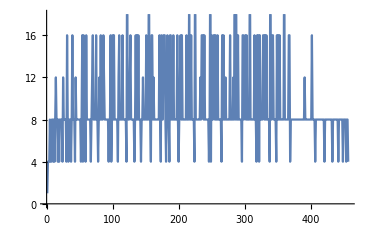

```mathematica
ListLinePlot[res]
```

```mathematica
√((0-64)^2+(35-33)^2)
```

√53

```mathematica
1/(√2-1)//N
```

2.41421